```mathematica
aboveColor=RGBColor[48/255,204/255,48/255];
belowColor=RGBColor[255/255,165/255,0/255];
(*belowColor=RGBColor[240/255,230/255,138/255];*)
fpColor=RGBColor[176/255,33/255,33/255];
lt=0.003;
```

```mathematica
fΔ1[ξ_,ϕ_,η_]:=1/4 √(16+(8 (1+2 η-ξ) ξ Sec[ϕ]^2+(-1+ξ)^2 Sec[ϕ]^4)/ξ^2);
f0[ξ_,ϕ_,η_]:=(1-ξ)/(4 (Cos[ϕ])^2 ξ);
fzp[ξ_,ϕ_,η_]:=f0[ξ,ϕ,η]+fΔ1[ξ,ϕ,η];
fzm[ξ_,ϕ_,η_]:=f0[ξ,ϕ,η]-fΔ1[ξ,ϕ,η];
fA2m[N_,ξ_,ϕ_,η_]:=Sum[Binomial[N,k] √(N-k)(√((1-fzm[ξ,ϕ,η])/2))^(2k+1)(√((1+fzm[ξ,ϕ,η])/2))^(2(N-k)-1),{k,0,N-1}]
fA2p[N_,ξ_,ϕ_,η_]:=Sum[Binomial[N,k] √(N-k)(√((1-fzp[ξ,ϕ,η])/2))^(2k+1)(√((1+fzp[ξ,ϕ,η])/2))^(2(N-k)-1),{k,0,N-1}]
xm[N_,ξ_,ϕ_,η_]:=fA2m[N,ξ,ϕ,η]Cos[ϕ]/√N;
pm[N_,ξ_,ϕ_,η_]:=fA2m[N,ξ,ϕ,η]Sin[ϕ]/√N;
xp[N_,ξ_,ϕ_,η_]:=fA2p[N,ξ,ϕ,η]Cos[ϕ]/√N;
pp[N_,ξ_,ϕ_,η_]:=fA2p[N,ξ,ϕ,η]Sin[ϕ]/√N;
(*xm[N_,ξ_,ϕ_,η_]:=fA2m[N,ξ,ϕ,η]Cos[ϕ];
pm[N_,ξ_,ϕ_,η_]:=fA2m[N,ξ,ϕ,η]Sin[ϕ];
xp[N_,ξ_,ϕ_,η_]:=fA2p[N,ξ,ϕ,η]Cos[ϕ];
pp[N_,ξ_,ϕ_,η_]:=fA2p[N,ξ,ϕ,η]Sin[ϕ];*)
```

```mathematica
q0=0.5;
plotlist={};
N0=50;
```

#### Separatrix

```mathematica
separatrix=ParametricPlot[{xm[N0,q0,ϕ,-1+q0+0.000001],pm[N0,q0,ϕ,-1+q0+0.000001]},{ϕ,-Pi,Pi},PlotRange->All,PlotStyle->Black];
AppendTo[plotlist,separatrix];
```

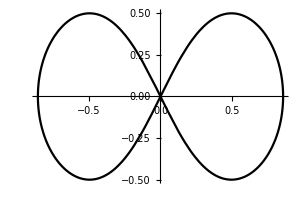

```mathematica
pic=Show[plotlist,Boxed->False,ImageSize->300,TicksStyle->Directive[FontSize->20]]
```

```mathematica
plotlist1=plotlist;
```

#### Above and below the separatrix

```mathematica
e0[q_,de_]:=Range[(-1-6 q-9 q^2)/(16 q)+de,-1+q-0.01,de]
e1[q_,de_]:=Range[-1+q+0.01,0-de,de];
```

```mathematica
de0=0.05;
de1=0.05;
```

#### Below

```mathematica
Do[
AppendTo[plotlist,ParametricPlot[{xm[N0,q0,ϕ,e],pm[N0,q0,ϕ,e]},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[lt],aboveColor],Exclusions->None]];
AppendTo[plotlist,ParametricPlot[{xp[N0,q0,ϕ,e],pp[N0,q0,ϕ,e]},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[lt],aboveColor],Exclusions->None]];
,{e,e0[q0,de0]}]
```

#### Plot

```mathematica
(*x1=N@Sum[Binomial[N0,k] √(N0-k)(√((1-1/4)/2))^(2k+1)(√((1+1/4)/2))^(2(N0-k)-1),{k,0,N0-1}];*)
x1=N@Sum[Binomial[N0,k] √(N0-k)(√((1-1/4)/2))^(2k+1)(√((1+1/4)/2))^(2(N0-k)-1),{k,0,N0-1}]/√N0;
stable1=ParametricPlot[{x1,0.0},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[0.03],fpColor],PlotPoints->100];
stable2=ParametricPlot[{-x1,0.0},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[0.03],fpColor],PlotPoints->100];
stable3=ParametricPlot[{0.0,0.0},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[0.03],fpColor],PlotPoints->100];
```

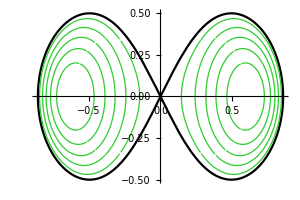

```mathematica
pic=Show[plotlist,stable1,stable2,stable3,Boxed->False,ImageSize->300,TicksStyle->Directive[FontSize->20]]
```

#### Above

```mathematica
Do[
AppendTo[plotlist,ParametricPlot[{xm[N0,q0,ϕ,e],pm[N0,q0,ϕ,e]},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[lt],belowColor]]];
,{e,e1[q0,de1]}]
```

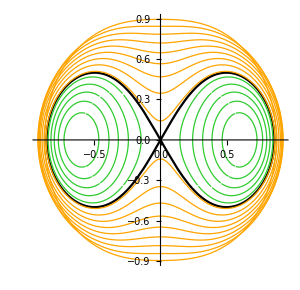

```mathematica
pic=Show[plotlist,stable1,stable2,stable3,Boxed->False,ImageSize->300,TicksStyle->Directive[FontSize->20]]
```

```mathematica
e2[q_,de_]:=Range[-0.05,-0.001,de];
de2=0.01;
Do[
AppendTo[plotlist1,ParametricPlot[{xm[N0,q0,ϕ,e],pm[N0,q0,ϕ,e]},{ϕ,-Pi,Pi},PlotStyle->Directive[Thickness[lt],belowColor]]];
,{e,e2[q0,de2]}]
```

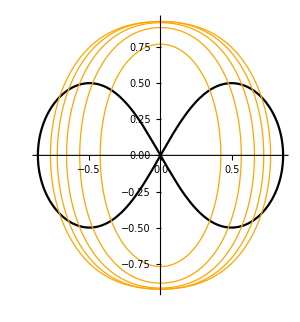

```mathematica
pic=Show[plotlist1,stable1,stable2,stable3,Boxed->False,ImageSize->300,TicksStyle->Directive[FontSize->20]]
```